```mathematica
<<TRQS`
```

Package TRQS version 0.0.8 (last modification: February 22, 2011).

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS

```mathematica
maxN = 7;
```

```mathematica
quantisNoHW=Table[{ii,AbsoluteTiming[Table[TrueRandomReal[],{10^ii}];][[1]]},{ii,1,maxN}]
Export["quantisNoHW.dat",quantisNoHW]
```

{{1,0.000365},{2,0.00284},{3,0.03176},{4,0.27854},{5,2.09595},{6,18.15167},{7,205.17081}}

quantisNoHW.dat

```mathematica
pseudo=Table[{ii,AbsoluteTiming[Table[RandomReal[];ClearSystemCache["Numeric"],{10^ii}];][[1]]},{ii,1,maxN}];
Export["pseudo.dat",pseudo]
```

pseudo.dat

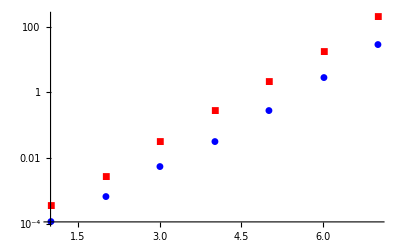

```mathematica
ListLogPlot[{pseudo,quantisNoHW},Joined->False,PlotStyle->{Blue,Red,Green},PlotMarkers->Automatic]
```